```mathematica
With[
{g=VertexDelete[Graph[plantri[[10]]],1]},
Table[
{Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding"],ColorsForEdgeOperationMatrix[g,{10<->11},op]},
{op,{EdgeContract,EdgeDelete}}
]
]
```

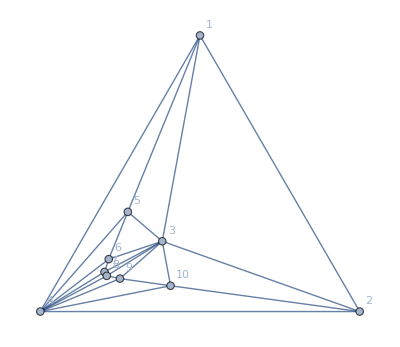

```mathematica
Graph[JacobsThalGraph2[10],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

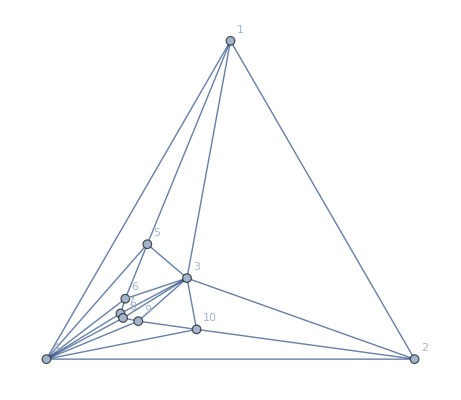
{-Graphics-,{{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2→ϵ | 2 | 2 | 2 | 3→2 | 3 | 3 | 3 | 3
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 3→ϵ
3 | 2 | 2→ϵ | 1 | 3→1 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2→ϵ | 3→1 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3→ϵ | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3→2 | 2→ϵ | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3→ϵ | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3→ϵ | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3→ϵ | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3→ϵ | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2→3 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2→3 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2→ϵ | 2 | 2 | 3→1 | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2→ϵ | 2 | 3→2 | 2 | 3→2 | 3→2 | 3→2 | 3→2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
4 | 2 | 2 | 3→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3→2 | 2→ϵ | 2 | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→1
10 | 3→1 | 2 | 2→ϵ | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→1 | 3→2 | 2→ϵ | 2 | 2 | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→2 | 2→ϵ | 2 | 3→1 | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2→ϵ | 2 | 3→2 | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→2 | 2→ϵ | 2 | 3→1 | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,3<->2}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2→3 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2→3 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,3<->2}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2→ϵ | 2 | 2 | 3→2 | 3→2 | 3→2 | 3→2 | 3→2
2 | 2 | 1 | 2→ϵ | 2 | 3→1 | 2 | 3→2 | 3→1 | 3→2 | 3→1
3 | 2→ϵ | 2→ϵ | 1→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
4 | 2 | 2 | 3→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3→1 | 2→ϵ | 2 | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→1
10 | 3→2 | 2 | 2→ϵ | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→2 | 3→2 | 2→ϵ | 2 | 2 | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2→ϵ | 2 | 3→1 | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→2 | 3→2 | 2→ϵ | 2 | 3→2 | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2→ϵ | 2 | 3→1 | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,3<->1}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2→3 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2→3 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,3<->1}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2→ϵ | 2 | 3→2 | 3→2 | 3→2 | 3→2 | 3→2
2 | 2 | 1 | 2 | 2→ϵ | 3→1 | 2 | 3→2 | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→ϵ | 2 | 2 | 2 | 2 | 2 | 2
4 | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 2 | 3→1 | 2 | 2→ϵ | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→1
10 | 3→2 | 2 | 2 | 2→ϵ | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→2 | 3→2 | 2 | 2→ϵ | 2 | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2 | 2→ϵ | 3→1 | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→2 | 3→2 | 2 | 2→ϵ | 3→2 | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2→ϵ | 3→1 | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,1<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2→3 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2→3 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,1<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2→ϵ | 2 | 3→1 | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2→ϵ | 3→2 | 2 | 3→2 | 3→2 | 3→2 | 3→2
3 | 2 | 2 | 1 | 3→ϵ | 2 | 2 | 2 | 2 | 2 | 2
4 | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 2 | 3→2 | 2 | 2→ϵ | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→1
10 | 3→1 | 2 | 2 | 2→ϵ | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→1 | 3→2 | 2 | 2→ϵ | 2 | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→2 | 2 | 2→ϵ | 3→1 | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2→ϵ | 3→2 | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→2 | 2 | 2→ϵ | 3→1 | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,2<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2→3 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2→3 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,2<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2→ϵ | 3 | 3→2 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3→ϵ | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3→1 | 2→ϵ | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→1 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2
5 | 2→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ
10 | 3 | 2 | 2 | 2 | 3→ϵ | 1 | 3 | 3 | 3 | 2
6 | 3→2 | 3 | 2 | 2 | 2→ϵ | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3→ϵ | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3→ϵ | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3→ϵ | 2 | 3 | 3 | 2 | 1){EdgeContract,5<->1}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2→3 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2→3 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,5<->1}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→ϵ | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2→ϵ | 3 | 3 | 3 | 3→2
3 | 2 | 2 | 1 | 3→1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→1 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3→ϵ | 2 | 3 | 3 | 3
10 | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ
6 | 3 | 3 | 2 | 2 | 2 | 3→ϵ | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3→ϵ | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3→ϵ | 3 | 2 | 1 | 2
9 | 3 | 3→2 | 2 | 2 | 3 | 2→ϵ | 3 | 3 | 2 | 1){EdgeContract,10<->2}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2→3 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2→3 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,10<->2}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→ϵ | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2→ϵ | 3→2 | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2→ϵ | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→ϵ | 2 | 3→1 | 3→2 | 3→1
10 | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→ϵ | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→ϵ | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→ϵ | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2→ϵ | 3→2 | 3→1 | 2 | 1){EdgeContract,10<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2→3 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2→3 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,10<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2→ϵ | 3→1 | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→ϵ | 2 | 3→2 | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2→ϵ | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2
5 | 2→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ
10 | 3→1 | 2 | 2 | 2 | 3→ϵ | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→1 | 3→2 | 2 | 2 | 2→ϵ | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→ϵ | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→ϵ | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→ϵ | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,5<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2→3 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2→3 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,5<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2→ϵ | 3→1 | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→ϵ | 2 | 3→2 | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2→ϵ | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2
5 | 2→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ
10 | 3→1 | 2 | 2 | 2 | 3→ϵ | 1 | 3→1 | 3→2 | 3→1 | 2
6 | 3→1 | 3→2 | 2 | 2 | 2→ϵ | 3→1 | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→ϵ | 3→2 | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→ϵ | 3→1 | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→ϵ | 2 | 3→2 | 3→1 | 2 | 1){EdgeContract,5<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2→3 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2→3 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,5<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3→ϵ | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3→ϵ | 3 | 3 | 3
3 | 2 | 2 | 1 | 3→1 | 2 | 2 | 2→ϵ | 2 | 2 | 2
4 | 2 | 2 | 3→1 | 1 | 2 | 2 | 2→ϵ | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2→ϵ | 3→2 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3→ϵ | 3 | 3 | 2
6 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 2→ϵ | 3→ϵ | 3→ϵ
7 | 3 | 3 | 2 | 2 | 3→2 | 3 | 2→ϵ | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3→ϵ | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3→ϵ | 3 | 2 | 1){EdgeContract,6<->5}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2→3 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2→3 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,6<->5}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→ϵ | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→ϵ | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2→ϵ | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2→ϵ | 2 | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2→ϵ | 3→1 | 3→2 | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→ϵ | 3→2 | 3→1 | 2
6 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 2→ϵ | 3→ϵ | 3→ϵ
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2→ϵ | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→ϵ | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→ϵ | 3→1 | 2 | 1){EdgeContract,6<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2→3 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2→3 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,6<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→ϵ | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→ϵ | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2→ϵ | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2→ϵ | 2 | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2→ϵ | 3→1 | 3→2 | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→ϵ | 3→2 | 3→1 | 2
6 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 2→ϵ | 3→ϵ | 3→ϵ
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2→ϵ | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→ϵ | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→ϵ | 3→1 | 2 | 1){EdgeContract,6<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2→3 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2→3 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,6<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3→ϵ | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3→ϵ | 3 | 3
3 | 2 | 2 | 1 | 3→1 | 2 | 2 | 2 | 2→ϵ | 2 | 2
4 | 2 | 2 | 3→1 | 1 | 2 | 2 | 2 | 2→ϵ | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3→ϵ | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3→ϵ | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2→ϵ | 3→2 | 3
7 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 3→ϵ
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3→2 | 2→ϵ | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3→ϵ | 2 | 1){EdgeContract,7<->6}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2→3 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2→3 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,7<->6}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→ϵ | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→ϵ | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2→ϵ | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2→ϵ | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→ϵ | 3→2 | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→ϵ | 3→1 | 2
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2→ϵ | 3→1 | 3→2
7 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 3→ϵ
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→1 | 2→ϵ | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→ϵ | 2 | 1){EdgeContract,7<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2→3 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2→3 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,7<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→ϵ | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→ϵ | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2→ϵ | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2→ϵ | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→ϵ | 3→2 | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→ϵ | 3→1 | 2
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2→ϵ | 3→1 | 3→2
7 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 3→ϵ
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→1 | 2→ϵ | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→ϵ | 2 | 1){EdgeContract,7<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2→3 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2→3 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,7<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3→ϵ | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3→ϵ | 3
3 | 2 | 2 | 1 | 3→1 | 2 | 2 | 2 | 2 | 2→ϵ | 2
4 | 2 | 2 | 3→1 | 1 | 2 | 2 | 2 | 2 | 2→ϵ | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3→ϵ | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3→ϵ | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3→ϵ | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2→ϵ | 3→2
8 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3→2 | 2→ϵ | 1){EdgeContract,8<->7}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2→3 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2→3 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,8<->7}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→2 | 3→ϵ | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 3→ϵ | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2 | 2→ϵ | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2 | 2→ϵ | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→1 | 3→ϵ | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→ϵ | 2
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2 | 3→ϵ | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2 | 1 | 2→ϵ | 3→1
8 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 2→ϵ | 1){EdgeContract,8<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2→3 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2→3 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,8<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→2 | 3→ϵ | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 3→ϵ | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2 | 2→ϵ | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2 | 2→ϵ | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→1 | 3→ϵ | 3→1
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→ϵ | 2
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2 | 3→ϵ | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2 | 1 | 2→ϵ | 3→1
8 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 2→ϵ | 1){EdgeContract,8<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2→3 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2→3 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,8<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3→ϵ
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3→ϵ
3 | 2 | 2 | 1 | 3→1 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
4 | 2 | 2 | 3→1 | 1 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3→ϵ
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3→2 | 2→ϵ
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3→ϵ
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3→ϵ
8 | 3 | 3 | 2 | 2 | 3 | 3→2 | 3 | 2 | 1 | 2→ϵ
9 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ){EdgeContract,9<->8}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2→3
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2→3 | 1){EdgeDelete,9<->8}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→2 | 3→1 | 3→ϵ
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 3→2 | 3→ϵ
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→ϵ
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2→ϵ
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2 | 3→1 | 3→ϵ
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2 | 1 | 2 | 3→ϵ
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→1 | 2 | 1 | 2→ϵ
9 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ){EdgeContract,9<->3}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2→3
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2→3 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,9<->3}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→1 | 3→1 | 3→2 | 3→1 | 3→ϵ
2 | 2 | 1 | 2 | 2 | 3→1 | 2 | 3→2 | 3→1 | 3→2 | 3→ϵ
3 | 2 | 2 | 1 | 3→2 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
4 | 2 | 2 | 3→2 | 1 | 2 | 2 | 2 | 2 | 2 | 2→ϵ
5 | 2 | 3→1 | 2 | 2 | 1 | 3→2 | 2 | 3→1 | 3→2 | 3→ϵ
10 | 3→1 | 2 | 2 | 2 | 3→2 | 1 | 3→1 | 3→2 | 3→1 | 2→ϵ
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→1 | 1 | 2 | 3→1 | 3→ϵ
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→2 | 2 | 1 | 2 | 3→ϵ
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→1 | 3→1 | 2 | 1 | 2→ϵ
9 | 3→ϵ | 3→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ | 1→ϵ){EdgeContract,9<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2→3
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2→3 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,9<->4}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→ϵ | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2→ϵ | 3 | 3 | 3 | 3→2
3 | 2 | 2 | 1 | 3→1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→1 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3→ϵ | 2 | 3 | 3 | 3
10 | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ
6 | 3 | 3 | 2 | 2 | 2 | 3→ϵ | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3→ϵ | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3→ϵ | 3 | 2 | 1 | 2
9 | 3 | 3→2 | 2 | 2 | 3 | 2→ϵ | 3 | 3 | 2 | 1){EdgeContract,10<->9}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 2→3
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2→3 | 3 | 3 | 2 | 1){EdgeDelete,10<->9}}},{{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3→ϵ | 3→1 | 3→2 | 3→1 | 3→2
2 | 2 | 1 | 2 | 2 | 3→1 | 2→ϵ | 3→2 | 3→1 | 3→2 | 3→1
3 | 2 | 2 | 1 | 3→2 | 2 | 2→ϵ | 2 | 2 | 2 | 2
4 | 2 | 2 | 3→2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2
5 | 2 | 3→1 | 2 | 2 | 1 | 3→ϵ | 2 | 3→1 | 3→2 | 3→1
10 | 3→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 1→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 2→ϵ
6 | 3→1 | 3→2 | 2 | 2 | 2 | 3→ϵ | 1 | 2 | 3→1 | 3→2
7 | 3→2 | 3→1 | 2 | 2 | 3→1 | 3→ϵ | 2 | 1 | 2 | 3→1
8 | 3→1 | 3→2 | 2 | 2 | 3→2 | 3→ϵ | 3→1 | 2 | 1 | 2
9 | 3→2 | 3→1 | 2 | 2 | 3→1 | 2→ϵ | 3→2 | 3→1 | 2 | 1){EdgeContract,10<->4}},{( | 1 | 2 | 3 | 4 | 5 | 10 | 6 | 7 | 8 | 9
1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3
2 | 2 | 1 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2
4 | 2 | 2 | 3 | 1 | 2 | 2→3 | 2 | 2 | 2 | 2
5 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 3 | 3 | 3
10 | 3 | 2 | 2 | 2→3 | 3 | 1 | 3 | 3 | 3 | 2
6 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 3 | 3
7 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 2 | 3
8 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 1 | 2
9 | 3 | 3 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 1){EdgeDelete,10<->4}}}}}

```mathematica
Monitor[
With[
{g=JacobsThalGraph2[10]},
{Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding"],
Table[ColorsForEdgeOperationMatrix[g,{e},op],{e,EdgeList[g]},{op,{EdgeContract,EdgeDelete}}]
}
],
{e,op}
]
```

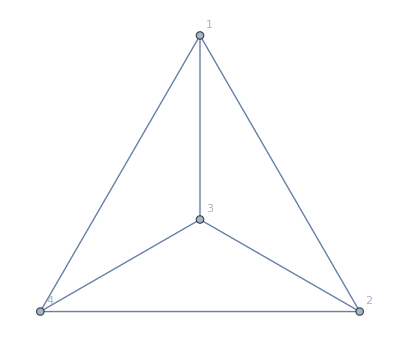
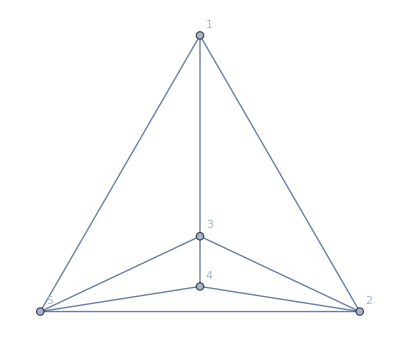
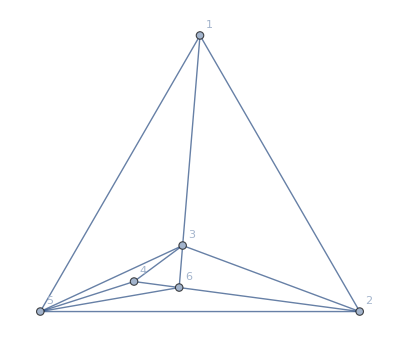
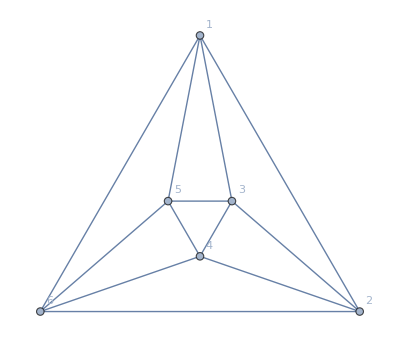
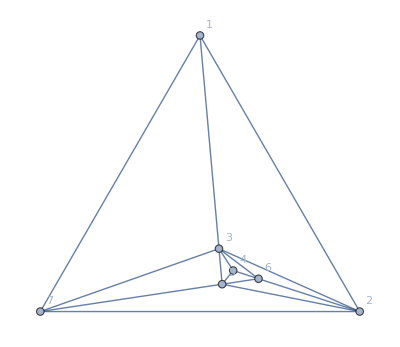
{{-Graphics-,{{{( | 1 | 2 | 3 | 4
1 | 1 | 2→ϵ | 2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2
4 | 2 | 2→ϵ | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 4
1 | 1 | 2→3 | 2 | 2
2 | 2→3 | 1 | 2 | 2
3 | 2 | 2 | 1 | 2
4 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 4
1 | 1 | 2 | 2→ϵ | 2
2 | 2 | 1 | 2→ϵ | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
4 | 2 | 2 | 2→ϵ | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 4
1 | 1 | 2 | 2→3 | 2
2 | 2 | 1 | 2 | 2
3 | 2→3 | 2 | 1 | 2
4 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 4
1 | 1 | 2 | 2 | 2→ϵ
2 | 2 | 1 | 2 | 2→ϵ
3 | 2 | 2 | 1 | 2→ϵ
4 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ){EdgeContract,1<->4}},{( | 1 | 2 | 3 | 4
1 | 1 | 2 | 2 | 2→3
2 | 2 | 1 | 2 | 2
3 | 2 | 2 | 1 | 2
4 | 2→3 | 2 | 2 | 1){EdgeDelete,1<->4}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2
5 | 2 | 2→ϵ | 2 | 1 | 2
4 | 1→2 | 2→ϵ | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3
2 | 2→3 | 1 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2
5 | 2 | 2 | 2 | 1 | 2
4 | 1→3 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2
2 | 2 | 1 | 2→ϵ | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
5 | 2 | 2 | 2→ϵ | 1 | 2
4 | 1→2 | 2 | 2→ϵ | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3
2 | 2 | 1 | 2 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2
5 | 2 | 2 | 2 | 1 | 2
4 | 1→3 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2
2 | 2 | 1 | 2 | 2→ϵ | 2
3 | 2 | 2 | 1 | 2→ϵ | 2
5 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
4 | 1→2 | 2 | 2 | 2→ϵ | 1){EdgeContract,1<->5}},{( | 1 | 2 | 3 | 5 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3
2 | 2 | 1 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2
5 | 2→3 | 2 | 2 | 1 | 2
4 | 1→3 | 2 | 2 | 2 | 1){EdgeDelete,1<->5}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2→1
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2
5 | 2 | 2→ϵ | 2 | 1 | 2 | 2
6 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2
4 | 2→1 | 1→ϵ | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2→3
2 | 2→3 | 1 | 2 | 2 | 2 | 1
3 | 2 | 2 | 1 | 2 | 2 | 2
5 | 2 | 2 | 2 | 1 | 2 | 2
6 | 1→3 | 2 | 2 | 2 | 1 | 2
4 | 2→3 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2
2 | 2 | 1 | 2→ϵ | 2 | 2 | 1
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 2 | 2 | 2→ϵ | 1 | 2 | 2
6 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2
4 | 2 | 1 | 2→ϵ | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 1
3 | 2→3 | 2 | 1 | 2 | 2 | 2
5 | 2 | 2 | 2 | 1 | 2 | 2
6 | 1→3 | 2 | 2 | 2 | 1 | 2
4 | 2 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 1
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2
5 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
6 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2
4 | 2 | 1 | 2 | 2→ϵ | 2 | 1){EdgeContract,1<->5}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 1
3 | 2 | 2 | 1 | 2 | 2 | 2
5 | 2→3 | 2 | 2 | 1 | 2 | 2
6 | 1→3 | 2 | 2 | 2 | 1 | 2
4 | 2 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->5}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2→ϵ | 2 | 2 | 2 | 3→2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 3→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 3→1 | 2
5 | 2 | 3→ϵ | 2 | 1 | 2 | 2
6 | 2 | 2→ϵ | 3→1 | 2 | 1 | 2
4 | 3→2 | 2→ϵ | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2→3 | 2 | 2 | 2 | 3
2 | 2→3 | 1 | 2 | 3 | 2 | 2
3 | 2 | 2 | 1 | 2 | 3 | 2
5 | 2 | 3 | 2 | 1 | 2 | 2
6 | 2 | 2 | 3 | 2 | 1 | 2
4 | 3 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2→ϵ | 2 | 2 | 3→2
2 | 2 | 1 | 2→ϵ | 3→1 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 3→ϵ | 2→ϵ
5 | 2 | 3→1 | 2→ϵ | 1 | 2 | 2
6 | 2 | 2 | 3→ϵ | 2 | 1 | 2
4 | 3→2 | 2 | 2→ϵ | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2→3 | 2 | 2 | 3
2 | 2 | 1 | 2 | 3 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 3 | 2
5 | 2 | 3 | 2 | 1 | 2 | 2
6 | 2 | 2 | 3 | 2 | 1 | 2
4 | 3 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→ϵ | 2 | 3→2
2 | 2 | 1 | 2 | 3→ϵ | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 3→1 | 2
5 | 2→ϵ | 3→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
6 | 2 | 2 | 3→1 | 2→ϵ | 1 | 2
4 | 3→2 | 2 | 2 | 2→ϵ | 2 | 1){EdgeContract,1<->5}},{( | 1 | 2 | 3 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→3 | 2 | 3
2 | 2 | 1 | 2 | 3 | 2 | 2
3 | 2 | 2 | 1 | 2 | 3 | 2
5 | 2→3 | 3 | 2 | 1 | 2 | 2
6 | 2 | 2 | 3 | 2 | 1 | 2
4 | 3 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->5}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 2→1
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 2
6 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2
4 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 2→3
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 1
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2
6 | 2 | 2 | 2 | 1 | 2 | 1 | 2
4 | 2→3 | 1 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 2
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 1
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 2
6 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2
4 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 1
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2
6 | 2 | 2 | 2 | 1 | 2 | 1 | 2
4 | 2 | 1 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 1
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 2
6 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2
4 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 6 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 1
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2
6 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2
4 | 2 | 1 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->7}}}}}}

```mathematica
Monitor[
Table[
With[
{g=ReadGrof[k]},
{Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding"],
Table[ColorsForEdgeOperationMatrix[g,{e},op],{e,Take[EdgeList[g],3]},{op,{EdgeContract,EdgeDelete}}]
}
],
{k,1,5}
],
{k,e,op}
]
```

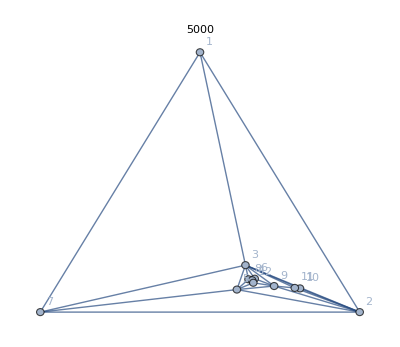
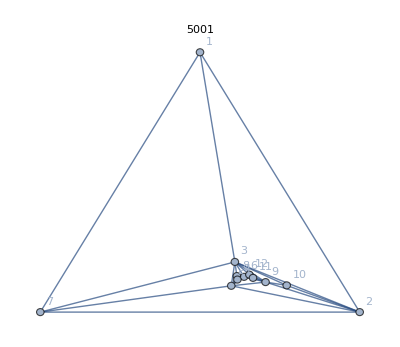
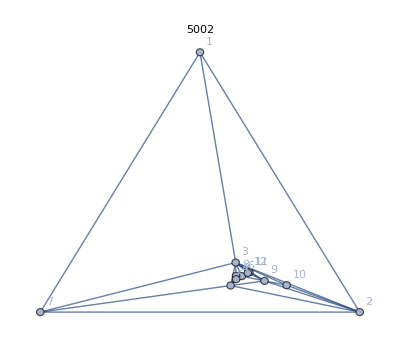
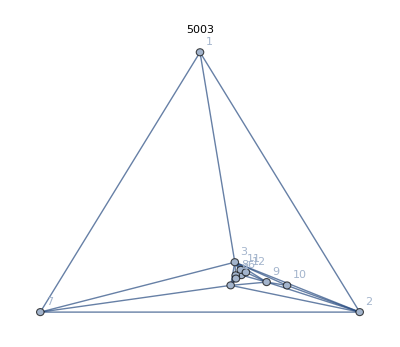
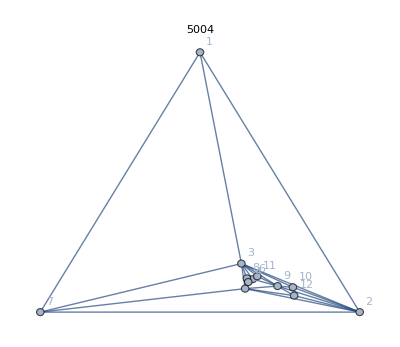
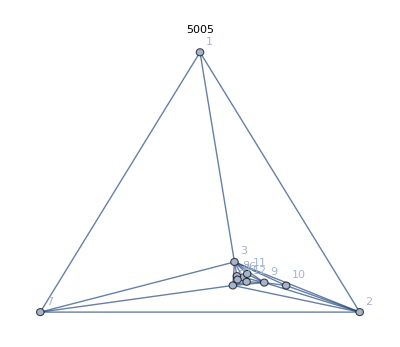
{{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 2 | 1→2 | 3 | 2→3 | 3 | 2→3
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 3→ϵ | 3→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3 | 3→ϵ | 2 | 2 | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2→3 | 3→ϵ | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3→ϵ | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2→3 | 3→ϵ | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 2 | 1→3 | 3 | 2→3 | 3 | 2→3
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
7 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2→3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2→3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 2 | 1→2 | 3→2 | 2 | 3 | 2→3
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3→2 | 3 | 2→ϵ | 2 | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2 | 3 | 2→ϵ | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3 | 3→ϵ | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2→3 | 3 | 3→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 2 | 1→3 | 3 | 2 | 3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
7 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2→3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 2→1 | 1→2 | 3→2 | 2→3 | 3 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 3→ϵ | 3→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3→2 | 3 | 2 | 2→ϵ | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2→3 | 3 | 2 | 3→ϵ | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3 | 3 | 3→ϵ | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2 | 3 | 3 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 11 | 6 | 8 | 4 | 12
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 2→3 | 1→3 | 3 | 2→3 | 3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
10 | 2→3 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 3 | 2 | 3 | 2
6 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 3 | 1 | 2 | 2 | 2
8 | 2→3 | 3 | 2 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 2 | 2
4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 1 | 2
12 | 2 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->7}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 1→2 | 2→1 | 2 | 1→2 | 2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 1→3 | 2→3 | 2 | 1→3 | 2 | 2
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 1→2 | 2 | 2 | 1→2 | 2→1 | 2→1
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 1→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 1→3 | 2 | 2 | 1→3 | 2→3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 1→2 | 2 | 2→1 | 1→2 | 2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 12 | 4 | 11
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 1→3 | 2 | 2→3 | 1→3 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
11 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->7}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 1→2 | 2→1 | 2 | 2→1 | 1→2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 1→3 | 2→3 | 2 | 2→3 | 1→3 | 2
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 1→2 | 2 | 2 | 2 | 1→2 | 2→1
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 1→3 | 2 | 2 | 2 | 1→3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 1→2 | 2 | 2→1 | 2 | 1→2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 1→3 | 2 | 2→3 | 2 | 1→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
8 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->7}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 1→2 | 2→1 | 2 | 2 | 1→2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 1→3 | 2→3 | 2 | 2 | 1→3 | 2
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 1→2 | 2 | 2 | 2 | 1→2 | 2→1
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 1→3 | 2 | 2 | 2 | 1→3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 1→2 | 2 | 2→1 | 2→1 | 1→2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 12 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 1→3 | 2 | 2→3 | 2→3 | 1→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
11 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2
12 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1){EdgeDelete,1<->7}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 1→2 | 2 | 2→1 | 2 | 1→2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 1→3 | 2 | 2→3 | 2 | 1→3 | 2
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 1→2 | 2→1 | 2 | 2 | 1→2 | 2→1
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 1→3 | 2→3 | 2 | 2 | 1→3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 1→2 | 2 | 2 | 2→1 | 1→2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 12 | 6 | 8 | 11 | 4
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 1→3 | 2 | 2 | 2→3 | 1→3 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
12 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2
8 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1){EdgeDelete,1<->7}}}}},{-Graphics-,{{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2→ϵ | 2 | 2 | 1→2 | 2 | 1→2 | 2→1 | 2 | 1→2 | 2 | 2
2 | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
3 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2→1 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→2 | 2→ϵ | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2 | 2→ϵ | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->2}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2→3 | 2 | 2 | 1→3 | 2 | 1→3 | 2→3 | 2 | 1→3 | 2 | 2
2 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2→3 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->2}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2 | 2→ϵ | 2 | 1→2 | 2 | 1→2 | 2 | 2 | 1→2 | 2→1 | 2→1
2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 1→ϵ
7 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→2 | 2 | 2→ϵ | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2→1 | 2 | 1→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->3}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2 | 2→3 | 2 | 1→3 | 2 | 1→3 | 2 | 2 | 1→3 | 2→3 | 2→3
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2→3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->3}}},{{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2 | 2 | 2→ϵ | 1→2 | 2→1 | 1→2 | 2 | 2→1 | 1→2 | 2 | 2
2 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 1→ϵ | 2→ϵ | 2→ϵ | 2→ϵ
5 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2→ϵ | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→1 | 2 | 2 | 1→ϵ | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→2 | 2 | 2 | 2→ϵ | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2 | 2 | 1 | 2→ϵ | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeContract,1<->7}},{( | 1 | 2 | 3 | 7 | 5 | 9 | 10 | 6 | 8 | 11 | 4 | 12
1 | 1 | 2 | 2 | 2→3 | 1→3 | 2→3 | 1→3 | 2 | 2→3 | 1→3 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
3 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
7 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
5 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
9 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
10 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
6 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
8 | 2→3 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2
11 | 1→3 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2
4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1
12 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1){EdgeDelete,1<->7}}}}}}

```mathematica
Monitor[
Table[
With[
{g=ReadGrof[m]},
{Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding",PlotLabel->m],
Table[ColorsForEdgeOperationMatrix[g,{e},op],{e,Take[EdgeList[g],3]},{op,{EdgeContract,EdgeDelete}}]
}
],
{m,5000,5005}
],
{m,e,op}
]
```

```mathematica
ReadGrof[300000]//VertexCount
```

14